```mathematica
Clear[hbar, e0, m0, ηm];
hbar=6.58211899*10^(-16);  (* h/2π  in eV s *)
m0=9.10938215*10^(-31); 
e0=1.602176487*10^(-19);
ηm=hbar^2*e0*10^(20)/m0;  (* hbar^2/m0 in eV A^2 *)
μB=5.7883818066 * 10^(-2);    (* in meV/T *)
meVpK=8.6173325*10^(-2);   (* Kelvin into meV *)
(* **************************************** *)
```

```mathematica
Clear[ts, tsw, as, ms, Nx, Ny, Nxn, α, αw, Δ];
as=100.0; (* unit cell in A *)
ms=0.02;
ts=500*ηm/(2*as^2*ms); (* hopping in meV *)
α=200.0/as; (* Rashba coupling in meV *)
Δ=0.4; (* induced gap in meV *)
Nx=100;
NxM=40;
Nxn=0;
Ny=1;
asw=600.0/(Ny+1);
αw=α*as/asw;
tsw=4.0;
μ=0.0;
B=2Δ;

(*
(*Turns off blue and red*)
tϕ1=0.4ts;
tϕ2=0.4ts;
tϕ3=0.4ts;
αϕ=0.0;
θ1=1.0π;
θM=0.1 π;
θ2=0.0 π;
θ3=0.5π;
*)

tϕ1=0.4ts;
tϕ2=0.4ts;
tϕ3=0.4ts;
αϕ=0.0;
θ1=1.0π;
θM=0.1 π;
θ2=0.5 π;
θ3=0.5π;

ϕ=0.5 π;
ϕ3=0;
```

```mathematica
ψA1L={};
ψAML={};
ψA2L={};
ψA3L={};

ψB1L={};
ψBML={};
ψB2L={};
ψB3L={};


For[θM=0,θM≤2 π,θM+=0.1,
ϵ0=2ts Cos[Pi/(Nx+1.0)];
(*First Chain*)
H1σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+B Sin[θ1],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H1σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-B Sin[θ1],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H1σ12τ11=SparseArray[{Band[{1,1}]->B Cos[θ1],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{Nx,Nx}];
H1σ21τ11=SparseArray[{Band[{1,1}]->B Cos[θ1],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{Nx,Nx}];

H1σ12τ12=SparseArray[{Band[{1,1}]->Δ},{Nx,Nx}];
H1σ21τ12=SparseArray[{Band[{1,1}]->-Δ},{Nx,Nx}];

H1τ11=SparseArray[ArrayFlatten[{{H1σ11τ11,H1σ12τ11},{H1σ21τ11,H1σ22τ11}}]];
H1τ22=-H1τ11;
H1τ12=SparseArray[ArrayFlatten[{{0,H1σ12τ12},{H1σ21τ12,0}}]];
H1τ21=Conjugate[Transpose[H1τ12]];

H11=SparseArray[ArrayFlatten[{{H1τ11,H1τ12},{H1τ21,H1τ22}}]];


(*Middle Chain*)
HMσ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+B Sin[θM],Band[{1,2}]->ts,Band[{2,1}]->ts},{NxM,NxM}];
HMσ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-B Sin[θM],Band[{1,2}]->ts,Band[{2,1}]->ts},{NxM,NxM}];
HMσ12τ11=SparseArray[{Band[{1,1}]->B Cos[θM],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{NxM,NxM}];
HMσ21τ11=SparseArray[{Band[{1,1}]->B Cos[θM],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{NxM,NxM}];

HMσ12τ12=SparseArray[{Band[{1,1}]->Δ ⅇ^(ⅈ ϕ)},{NxM,NxM}];
HMσ21τ12=SparseArray[{Band[{1,1}]->-Δ ⅇ^(ⅈ ϕ)},{NxM,NxM}];

HMτ11=SparseArray[ArrayFlatten[{{HMσ11τ11,HMσ12τ11},{HMσ21τ11,HMσ22τ11}}]];
HMτ22=-HMτ11;
HMτ12=SparseArray[ArrayFlatten[{{0,HMσ12τ12},{HMσ21τ12,0}}]];
HMτ21=Conjugate[Transpose[HMτ12]];

HMM=SparseArray[ArrayFlatten[{{HMτ11,HMτ12},{HMτ21,HMτ22}}]];


(*Second Chain*)
H2σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+B Sin[θ2],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H2σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-B Sin[θ2],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H2σ12τ11=SparseArray[{Band[{1,1}]->B Cos[θ2],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{Nx,Nx}];
H2σ21τ11=SparseArray[{Band[{1,1}]->B Cos[θ2],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{Nx,Nx}];

H2σ12τ12=SparseArray[{Band[{1,1}]->Δ ⅇ^(ⅈ ϕ)},{Nx,Nx}];
H2σ21τ12=SparseArray[{Band[{1,1}]->-Δ ⅇ^(ⅈ ϕ)},{Nx,Nx}];

H2τ11=SparseArray[ArrayFlatten[{{H2σ11τ11,H2σ12τ11},{H2σ21τ11,H2σ22τ11}}]];
H2τ22=-H2τ11;
H2τ12=SparseArray[ArrayFlatten[{{0,H2σ12τ12},{H2σ21τ12,0}}]];
H2τ21=Conjugate[Transpose[H2τ12]];

H22=SparseArray[ArrayFlatten[{{H2τ11,H2τ12},{H2τ21,H2τ22}}]];

(*Third Chain*)
H3σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+B Sin[θ3],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H3σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-B Sin[θ3],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H3σ12τ11=SparseArray[{Band[{1,1}]->ⅈ B Cos[θ3],Band[{1,2}]->-ⅈ α/2,Band[{2,1}]->ⅈ α/2},{Nx,Nx}];
H3σ21τ11=SparseArray[{Band[{1,1}]->-ⅈ B Cos[θ3],Band[{1,2}]->-ⅈ α/2,Band[{2,1}]->ⅈ α/2},{Nx,Nx}];

H3σ12τ12=SparseArray[{Band[{1,1}]->ⅈ Δ ⅇ^(ⅈ ϕ3)},{Nx,Nx}];
H3σ21τ12=SparseArray[{Band[{1,1}]->ⅈ Δ ⅇ^(ⅈ ϕ3)},{Nx,Nx}];

H3τ11=SparseArray[ArrayFlatten[{{H3σ11τ11,H3σ12τ11},{H3σ21τ11,H3σ22τ11}}]];
H3τ22=-H3τ11;
H3τ12=SparseArray[ArrayFlatten[{{0,H3σ12τ12},{H3σ21τ12,0}}]];
H3τ21=Conjugate[Transpose[H3τ12]];

H33=SparseArray[ArrayFlatten[{{H3τ11,H3τ12},{H3τ21,H3τ22}}]];

(*Tunnel Junction*)
H1M=SparseArray[{{Nx,1}->tϕ1,{2Nx,NxM+1}->tϕ1,{3Nx,2NxM+1}->-tϕ1,{4Nx,3NxM+1}->-tϕ1},{4Nx,4NxM}];
HM1=Conjugate[Transpose[H1M]];

HM2=SparseArray[{{NxM,1}->tϕ2,{2NxM,Nx+1}->tϕ2,{3NxM,2Nx+1}->-tϕ2,{4NxM,3Nx+1}->-tϕ2},{4NxM,4Nx}];
H2M=Conjugate[Transpose[HM2]];

HM3=SparseArray[{{NxM/2,1}->tϕ3,{NxM+NxM/2,Nx+1}->tϕ3,{2NxM+NxM/2,2Nx+1}->-tϕ3,{3NxM+NxM/2,3Nx+1}->-tϕ3},{4NxM,4Nx}];
H3M=Conjugate[Transpose[HM3]];

(*Full Wire*)
Hsp=SparseArray[ArrayFlatten[{{H11,H1M,0,0},{HM1,HMM,HM2,HM3},{0,H2M,H22,0},{0,H3M,0,H33}}]];

{e,ψ}=Transpose[Sort[Transpose[Eigensystem[Hsp,-10]]]];



n=5;
Print[{θM,e[[n]],e[[n-1]]}];
ψA1ue=Table[{i-1,Abs[ψ[[n,i]]]},{i,1,Nx}];
ψAMue=Table[{i-1-3Nx,Abs[ψ[[n,i]]]},{i,4Nx,4Nx+NxM}];
ψA2ue=Table[{i-1-3Nx-3NxM,Abs[ψ[[n,i]]]},{i,4Nx+4NxM,4Nx+4NxM+Nx}];
ψA3ue=Table[{i-1-3Nx-3NxM-3Nx,Abs[ψ[[n,i]]]},{i,4Nx+4NxM+4Nx,4Nx+4NxM+4Nx+Nx}];




e[[n-1]];
ψB1ue=Table[{i-1,Abs[ψ[[n-1,i]]]},{i,1,Nx}];
ψBMue=Table[{i-1-3Nx,Abs[ψ[[n-1,i]]]},{i,4Nx,4Nx+NxM}];
ψB2ue=Table[{i-1-3Nx-3NxM,Abs[ψ[[n-1,i]]]},{i,4Nx+4NxM,4Nx+4NxM+Nx}];
ψB3ue=Table[{i-1-3Nx-3NxM-3Nx,Abs[ψ[[n-1,i]]]},{i,4Nx+4NxM+4Nx,4Nx+4NxM+4Nx+Nx}];

ψA1L=Join[ψA1L,{ψA1ue}];
ψAML=Join[ψAML,{ψAMue}];
ψA2L=Join[ψA2L,{ψA2ue}];
ψA3L=Join[ψA3L,{ψA3ue}];

ψB1L=Join[ψB1L,{ψB1ue}];
ψBML=Join[ψBML,{ψBMue}];
ψB2L=Join[ψB2L,{ψB2ue}];
ψB3L=Join[ψB3L,{ψB3ue}];

];
```

{0,-0.0000692569,-0.00118519}

{0.1,-0.0000699303,-0.0011771}

{0.2,-0.0000691591,-0.00116735}

{0.3,-0.0000666163,-0.00115643}

{0.4,-0.0000624736,-0.00114536}

{0.5,-0.0000573238,-0.0011352}

{0.6,-0.0000518605,-0.00112653}

{0.7,-0.0000466114,-0.00111945}

{0.8,-0.0000418647,-0.0011138}

{0.9,-0.0000377221,-0.00110936}

{1.,-0.0000341773,-0.00110594}

{1.1,-0.0000311749,-0.00110339}

{1.2,-0.0000286438,-0.00110162}

{1.3,-0.0000265143,-0.00110057}

{1.4,-0.000024724,-0.0011002}

{1.5,-0.0000232203,-0.00110047}

{1.6,-0.0000219596,-0.00110137}

{1.7,-0.0000209067,-0.00110289}

{1.8,-0.0000200331,-0.001105}

{1.9,-0.0000193162,-0.00110768}

{2.,-0.0000187379,-0.00111093}

{2.1,-0.0000182844,-0.00111471}

{2.2,-0.0000179451,-0.00111901}

{2.3,-0.0000177122,-0.00112378}

{2.4,-0.0000175807,-0.00112899}

{2.5,-0.0000175477,-0.00113461}

{2.6,-0.0000176125,-0.00114058}

{2.7,-0.0000177768,-0.00114685}

{2.8,-0.0000180446,-0.00115336}

{2.9,-0.0000184223,-0.00116006}

{3.,-0.0000189193,-0.00116686}

{3.1,-0.0000195482,-0.0011737}

{3.2,-0.000020326,-0.00118049}

{3.3,-0.0000212745,-0.00118715}

{3.4,-0.0000224223,-0.00119358}

{3.5,-0.0000238062,-0.00119969}

{3.6,-0.0000254738,-0.00120535}

{3.7,-0.0000274874,-0.00121046}

{3.8,-0.0000299283,-0.00121488}

{3.9,-0.0000329029,-0.00121845}

{4.,-0.0000365499,-0.00122102}

{4.1,-0.0000410467,-0.00122235}

{4.2,-0.0000466089,-0.00122221}

{4.3,-0.0000534661,-0.00122035}

{4.4,-0.0000617682,-0.0012166}

{4.5,-0.0000713418,-0.00121122}

{4.6,-0.0000812319,-0.00120548}

{4.7,-0.000089338,-0.00120203}

{4.8,-0.000093183,-0.0012034}

{4.9,-0.0000919824,-0.00120911}

{5.,-0.0000873247,-0.00121594}

{5.1,-0.0000814588,-0.00122123}

{5.2,-0.0000758722,-0.00122412}

{5.3,-0.0000712002,-0.00122482}

{5.4,-0.0000676001,-0.00122381}

{5.5,-0.0000650357,-0.00122157}

{5.6,-0.0000634163,-0.00121846}

{5.7,-0.0000626487,-0.00121475}

{5.8,-0.000062649,-0.00121064}

{5.9,-0.0000633333,-0.00120623}

{6.,-0.000064593,-0.00120156}

{6.1,-0.0000662548,-0.0011965}

{6.2,-0.0000680257,-0.00119078}

```mathematica
1.2/π
```

0.381972

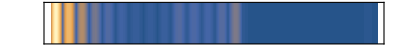

```mathematica
nt=48;
ψbar=Join[ψA1L[[nt]],ψAML[[nt]],ψA2L[[nt]]];
ψbarC=Join[Table[{i,0.0,ψbar[[i,2]]},{i,1,Length[ψbar]}],Table[{i,1.0,ψbar[[i,2]]},{i,1,Length[ψbar]}]];
bar=ListContourPlot[ψbarC,PlotRange->{0,0.1},Contours->100,ContourStyle->None,AspectRatio->1/10,FrameTicks->None]
```

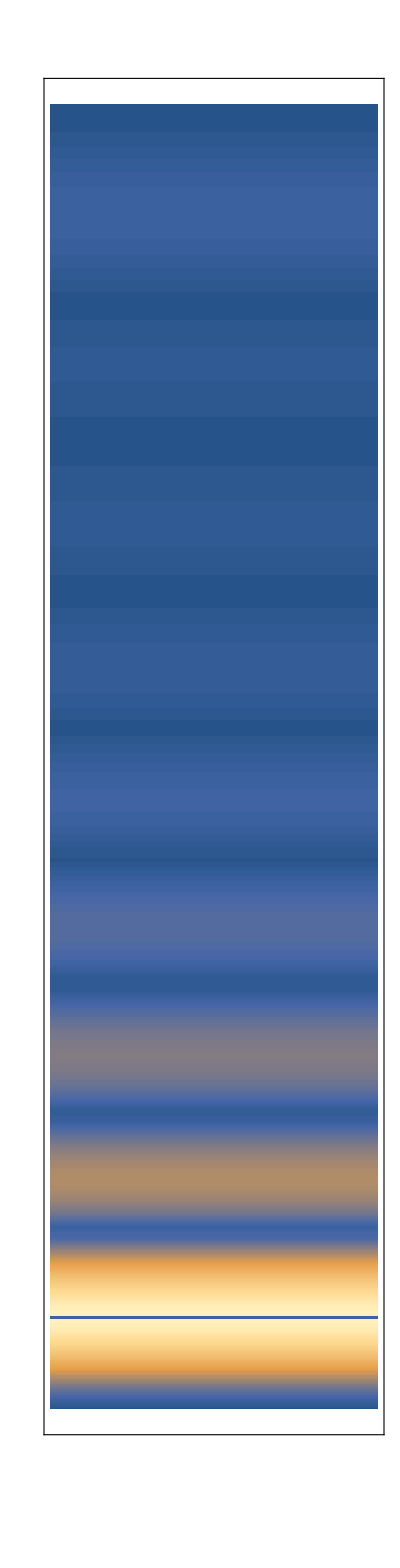

```mathematica
nt=48;
ψleg=ψA3L[[nt]];
ψlegC=Join[Table[{0.0,Length[ψleg]-i,ψleg[[i,2]]},{i,1,Length[ψleg]}],Table[{1.0,Length[ψleg]-i,ψleg[[i,2]]},{i,1,Length[ψleg]}]];
leg=ListContourPlot[ψlegC,PlotRange->{0,0.1},Contours->100,ContourStyle->None,AspectRatio->10/1,FrameTicks->None]
```

```mathematica
Manipulate[ListPlot[{ψA1L[[nt]],ψAML[[nt]],ψA2L[[nt]],ψA3L[[nt]]},Joined->True,PlotRange->All],{nt,1,Length[ψA1L],1}]
```

```mathematica
Manipulate[ListPlot[{ψB1L[[nt]],ψBML[[nt]],ψB2L[[nt]],ψB3L[[nt]]},Joined->True,PlotRange->All],{nt,1,Length[ψB1L],1}]
```